```mathematica
(* step 1: Import fort.14 *)
```

```mathematica
(*reads xyz as lat/longs*)
(*Memory use: on the order of 10* size of grid, i.e. 340 MB for v6brivers*)
Off[General::partw];
gridfilepath="C:\\Users\\Sam\\Dropbox\\ADCIRC\\base grid\\fort.14";
maxelepath="C:\\Users\\Sam\\Dropbox\\irene\\hurricane\\maxele.63";
slam0=-79.0;(*center longitude*)
sfea0=35.0;(*center latitude*)
NAN="NAN";(*Designator for non-values*)
restart=0;
d2r=3.14159265358979323/180;
R=6378206.4;
slam0r=slam0*d2r;
sfea0r=sfea0*d2r;
```

```mathematica
fort14=OpenRead[gridfilepath];
gridname=ToExpression[Read[fort14,Word]];
ne=ToExpression[Read[fort14,Number]];
nn=ToExpression[Read[fort14,Number]];

XYZ=Table[{NAN,NAN,NAN},{nn}];
ELNODES=Table[{NAN,NAN,NAN},{ne}]; (*for elnodes*)

Do[
Read[fort14,Number];
lon=Read[fort14,Number];
lat=Read[fort14,Number];
XYZ[[i,3]]=Read[fort14,Number];

(*convert to cartesian from spherical*)
slam=lon*d2r;
XYZ[[i,1]]=R*(slam-slam0r)*Cos[sfea0r];

sfea=lat*d2r;
XYZ[[i,2]]=R*sfea;
,{i,1,nn}];

Do[
Read[fort14,Number];
Read[fort14,Number];
ELNODES[[i]]=ReadList[fort14,Number,3];
,{i,1,ne}];
Close[fort14];
```

```mathematica
ELBOUNDS=Table[NAN,{ne}];

Do[
nodenums=ELNODES[[i]];

xmax=-9999999;
ymax=-9999999;
xmin=9999999;
ymin=9999999;


Do[
xtemp=XYZ[[nodenums[[j]],1]];
ytemp=XYZ[[nodenums[[j]],2]];
If[xtemp>xmax,xmax=xtemp];
If[ytemp>ymax,ymax=ytemp];
If[xtemp<xmin,xmin=xtemp];
If[ytemp<ymin,ymin=ytemp];
,{j,1,3}];

ELBOUNDS[[i]]={xmax,ymax,xmin,ymin};
,{i,1,ne}];
```

```mathematica
gridx=Transpose[XYZ][[1]];
gridy=Transpose[XYZ][[2]];
gridz=Transpose[XYZ][[3]];

ListPlot[Transpose[Table[{gridx,gridy}]],PlotRange->Full]
```

-Graphics-

```mathematica
(*Step 2. Read in points of interest*)
stnlist=OpenRead["C:\\Users\\Sam\\Dropbox\\irene\\observed stage\\hwms\\hwm locations long lat.txt"];
l=ReadList[stnlist,Number];
Close[stnlist];
stationlatlon=Partition[l,2];
nstations=Length[stationlatlon];


stationXYZ=Table[{NAN,NAN,NAN},{nstations}];
Do[
lon=stationlatlon[[i]][[1]];
lat=stationlatlon[[i]][[2]];

slam=lon*d2r;
stationXYZ[[i,1]]=R*(slam-slam0r)*Cos[sfea0r];

sfea=lat*d2r;
stationXYZ[[i,2]]=R*sfea;
,{i,1,nstations}];


stax=Transpose[stationXYZ][[1]];
stay=Transpose[stationXYZ][[2]];

Show[ListPlot[Transpose[Table[{gridx,gridy}]],PlotRange->Full],ListPlot[Transpose[Table[{stax,stay}]],PlotStyle->Red]]
```

-Graphics-

```mathematica
(* step 3 - find list of possible elements*)
(*reduce grid to tenable numbers*)
(*use Max[stax]/[stay]/etc for auto-calculating.*)
If[restart==0,

xmax=Max[stax]+1000;
ymax=Max[stay]+1000;
xmin=Min[stax]+1000;
ymin=Min[stay]+1000;
(*
xmax=185000;
ymax=4.00*10^6;
xmin=130000;
ymin=3.94*10^6;
*)

(*find elements that are within bounds. in v6brivers, this cuts elements from 575512 to 22897 in <4s*)
inlist={};
Do[
If[ELBOUNDS[[i]][[1]]<xmax+500,
If[ELBOUNDS[[i]][[2]]<ymax+500,
If[ELBOUNDS[[i]][[3]]>xmin-500,
If[ELBOUNDS[[i]][[4]]>ymin-500,
inlist=Flatten[Append[inlist,i]];
]]]],{i,1,ne}];];
```

```mathematica
Max[inlist]
```

539006

```mathematica
Length[ELNODES]
```

575512

337346

169442

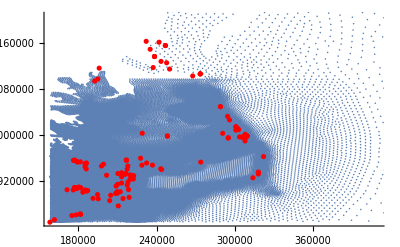

restart selected

NullNull

```mathematica
(*check to ensure reduced grid contains all stations*)
l1=Length[inlist]
innodes=Union[Flatten[Table[ELNODES[[inlist[[i]]]],{i,1,l1}]]];
l2=Length[innodes]
x=Table[XYZ[[innodes[[i]],1]],{i,1,l2}];
y=Table[XYZ[[innodes[[i]],2]],{i,1,l2}];
Show[ListPlot[Transpose[Table[{x,y}]]],ListPlot[Transpose[Table[{stax,stay}]],PlotStyle->Red,PlotRange->Full]]
Print[
,
Print["restart selected"];
];
```

```mathematica
7
```

```mathematica
(*step 4: find possible elements for each station, then do point-in-polygon to find correct station*)
If[restart==0,




nesub=Length[inlist];
stationElement=Table[NAN,{nstations}];

Do[
(*for each station*)
p={stax[[i]],stay[[i]]};

(*PIP algorithm*)
Do[
(*for each station and for each possible element*)
nodestemp=ELNODES[[inlist[[j]]]];
a=nodestemp[[1]];
b=nodestemp[[2]];
c=nodestemp[[3]];
a={XYZ[[a]][[1]],XYZ[[a]][[2]]};
b={XYZ[[b]][[1]],XYZ[[b]][[2]]};
c={XYZ[[c]][[1]],XYZ[[c]][[2]]};
(*compute vectors*)
v0=c-a;
v1=b-a;
v2=p-a;
(* compute dot products*)
dot00=Dot[v0,v0];
dot01=Dot[v0,v1];
dot02=Dot[v0,v2];
dot11=Dot[v1,v1];
dot12=Dot[v1,v2];
(*compute barycentric coordinates*)
invDenom=1/((dot00*dot11)-(dot01*dot01));
u=(dot11*dot02-dot01*dot12)*invDenom;
v=(dot00*dot12-dot01*dot02)*invDenom;
(*check if point is in triangle*)
If[u≥0∧v≥0∧(u+v)<1,
(*point is in triangle*)
stationElement[[i]]=inlist[[j]];
Break[];
];(* end of if *)



,{j,1,nesub}];


,{i,1,nstations}];

Export["C:\\Users\\Sam\\Dropbox\\ADCIRC\\Data reading - HWMs\\stationElement.txt",stationElement];
,
Print["restart selected"];
in=OpenRead["C:\\Users\\Sam\\Dropbox\\ADCIRC\\Data reading - HWMs\\stationElement.txt"];
stationElement={};
Do[
stationElement=Append[stationElement,Read[in]];
,{nstations}]
];
```

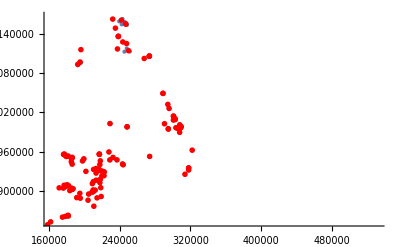

```mathematica
(*validate search algorithm*)
stationElementClean=Delete[stationElement,Position[stationElement,"NAN"]];
stationNodes=Flatten[Table[ELNODES[[stationElementClean[[i]]]],{i,1,Length[stationElementClean]}]];
stationNodes=Union[stationNodes];
stationNodeXYZ=Table[XYZ[[stationNodes[[i]]]],{i,1,Length[stationNodes]}];


x=Transpose[stationNodeXYZ][[1]];
y=Transpose[stationNodeXYZ][[2]];
Show[ListPlot[Transpose[Table[{x,y}]]],ListPlot[Transpose[Table[{stax,stay}]],PlotStyle->Red,PlotRange->Full,PlotMarkers->Tiny]]
```

```mathematica
Max[{maxel[[1,2]],maxel[[1,7]]}]
```

0.875633

General::stream: -- Message text not found -- ($Failed)

General::stop: Further output of General :: stream will be suppressed during this calculation.

OpenRead::noopen: -- Message text not found -- ("C:\\Users\\Sam\\Dropbox\\irene\\hurricane\\maxele.63")

OpenRead::noopen: -- Message text not found -- ("C:\\Program Files\\Wolfram Research\\Mathematica\\10.1\\Documentation\\English\\PacletDB.m")

General::stop: Further output of OpenRead :: noopen will be suppressed during this calculation.

Table::iterb: -- Message text not found -- ({Read[$Failed, Number]})

Do::iterb: -- Message text not found -- ({i, 1, np$7270})

Table::iterb: -- Message text not found -- ({Read[$Failed, Number]})

General::stop: Further output of Table :: iterb will be suppressed during this calculation.

Do::iterb: -- Message text not found -- ({i, 1, np$12481})

General::stop: Further output of Do :: iterb will be suppressed during this calculation.

General::stream: -- Message text not found -- ($Failed)

General::stop: Further output of General :: stream will be suppressed during this calculation.

OpenRead::noopen: -- Message text not found -- ("C:\\Program Files\\Wolfram Research\\Mathematica\\10.1\\Documentation\\English\\PacletDB.m")

OpenWrite::noopen: -- Message text not found -- ("C:\\Users\\Sam\\Dropbox\\ADCIRC\\Data reading - HWMs\\hwm elev.txt")

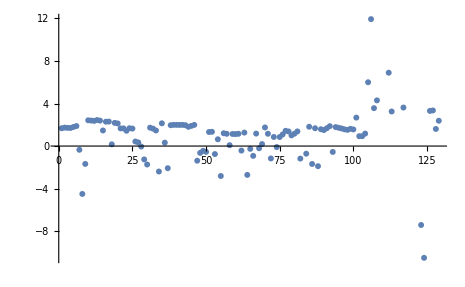

```mathematica
(*interpolate bathymetry at each station*)
(*linear expansion of Z term, following methods in theory discussion (below)*)
(*comment for bathy interp*)
maxel=ReadMaxAll[maxelepath];
XYZ=Transpose[XYZ];
Do[
XYZ[[3,i]]=Max[maxel[[1,i]],XYZ[[3,i]]];
,{i,1,Length[XYZ[[3]]]}]
XYZ=Transpose[XYZ];

stationBathy=Table[NAN,{nstations}];
Do[

If[stationElement[[i]]=="NAN",
(*do nothing*)
,
(*else perform linear interpolation between bounding element's nodal values*)
x=stax[[i]];
y=stay[[i]];

xyz1=XYZ[[ELNODES[[stationElement[[i]]]][[1]]]];
xyz2=XYZ[[ELNODES[[stationElement[[i]]]][[2]]]];
xyz3=XYZ[[ELNODES[[stationElement[[i]]]][[3]]]];

x1=xyz1[[1]];
x2=xyz2[[1]];
x3=xyz3[[1]];
y1=xyz1[[2]];
y2=xyz2[[2]];
y3=xyz3[[2]];
z1=xyz1[[3]];
z2=xyz2[[3]];
z3=xyz3[[3]];

b1=y2-y3;
b2=y3-y1;
b3=y1-y2;
a1=x3-x2;
a2=x1-x3;
a3=x2-x1;
elA=(b1*a2-b2*a1)/2;


p1=(x2*y3-x3*y2+b1*x+a1*y)/(2*elA);
p2=(x3*y1-x1*y3+b2*x+a2*y)/(2*elA);
p3=(x1*y2-x2*y1+b3*x+a3*y)/(2*elA);

stationBathy[[i]]=p1*z1+p2*z2+p3*z3;
];
,{i,1,nstations}];

Export["C:\\Users\\Sam\\Dropbox\\ADCIRC\\Data reading - HWMs\\hwm elev.txt",stationBathy];
ListPlot[stationBathy,PlotRange->Full]
```

```mathematica
XYZ[[3]]
```

{1.72889×10^6,976151.,25.354}

-Graphics-